```mathematica
inferedConnection=ToExpression@StringReplace["[[0, 0], [1, 0], [2, 0], [3, 0], [4, 0], [5, 0], [6, 0], [7, 0], [8, 0], [2, 1], [3, 1], [4, 1], [0, 2], [1, 2], [2, 2], [5, 2], [8, 2], [0, 3], [1, 3], [3, 3], [5, 3], [8, 3], [5, 4], [2, 5], [3, 5], [4, 5], [6, 5], [7, 5], [1, 6], [6, 6], [8, 6], [1, 7], [7, 7], [8, 7], [4, 8], [0, 2], [0, 3], [1, 6], [1, 7], [2, 1], [2, 2], [3, 1], [3, 3], [4, 8], [5, 4], [6, 6], [7, 7], [8, 6], [8, 7]]",{"["->"{","]"->"}"}];
```

```mathematica
cnnInfered2=Normal@SparseArray[Thread[Select[Tally[inferedConnection],#⟦2⟧==2&]ᵀ⟦1⟧+1->1]]
```

{{0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,1,1,0},{0,1,1,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,1,0}}

```mathematica
realConnection=ToExpression@StringReplace["[[0, 0], [0, 0], [0, 2], [0, 3], [1, 1], [2, 1], [3, 1], [4, 1], [1, 1], [1, 2], [1, 3], [1, 6], [1, 7], [0, 2], [1, 2], [2, 2], [5, 2], [8, 2], [2, 1], [2, 2], [2, 5], [0, 3], [1, 3], [3, 3], [5, 3], [8, 3], [3, 1], [3, 3], [3, 5], [4, 4], [5, 4], [4, 1], [4, 4], [4, 5], [4, 8], [2, 5], [3, 5], [4, 5], [5, 5], [6, 5], [7, 5], [5, 2], [5, 3], [5, 4], [5, 5], [8, 6], [1, 6], [6, 6], [6, 5], [6, 6], [8, 7], [1, 7], [7, 7], [7, 5], [7, 7], [8, 8], [4, 8], [8, 2], [8, 3], [8, 6], [8, 7], [8, 8]]",{"["->"{","]"->"}"}];
```

```mathematica
cnnInfered=Normal@SparseArray[Thread[inferedConnection+1->1]]
```

{{1,0,1,1,0,0,0,0,0},{1,0,1,1,0,0,1,1,0},{1,1,1,0,0,1,0,0,0},{1,1,0,1,0,1,0,0,0},{1,1,0,0,0,1,0,0,1},{1,0,1,1,1,0,0,0,0},{1,0,0,0,0,1,1,0,0},{1,0,0,0,0,1,0,1,0},{1,0,1,1,0,0,1,1,0}}

```mathematica
cnnReal=Normal@SparseArray[Thread[realConnection+1->1]]
```

{{1,0,1,1,0,0,0,0,0},{0,1,1,1,0,0,1,1,0},{0,1,1,0,0,1,0,0,0},{0,1,0,1,0,1,0,0,0},{0,1,0,0,1,1,0,0,1},{0,0,1,1,1,1,0,0,0},{0,0,0,0,0,1,1,0,0},{0,0,0,0,0,1,0,1,0},{0,0,1,1,0,0,1,1,1}}

```mathematica
1-N@((Total@Flatten@Abs[cnnInfered-cnnReal])/Length[cnnInfered]^2)
```

0.851852

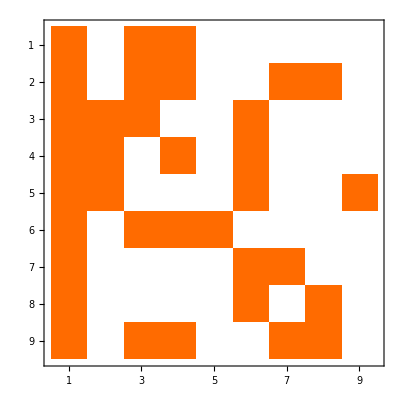

```mathematica
MatrixPlot[cnnInfered]
```

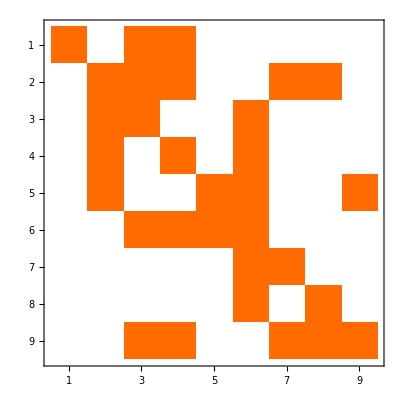

```mathematica
MatrixPlot[cnnReal]
```